# Modèle 0 : Ravageur Uniquement

## Présentation du modèle

```mathematica
ModeleComplet = {
U'[t] == q  A[t] - q δa A[t-τu] Exp[-δu τu]  - δu U[t],
L'[t] == q  A[t-τu] Exp[-δu τu]- q A[t-τu-τl] Exp[-δu τu] H[t] -  (δl+αl L[t]) L[t],
M'[t] == q  A[t-τu-τl] Exp[-δu τu]H[t] -  q  A[t-τu-τl-τm] Exp[-δu τu] H[t- τm]Exp[-δm τm] -  δm M[t],
A'[t] == q  A[t-τu-τl-τm] Exp[-δu τu] H[t- τm]Exp[-δm τm] -δa A[t],
H'[t] ==-αl H[t](L[t]-L[t-τl])
}
```

{U'[t]==q A[t]-0.1 ⅇ^(-δu τu) q A[t-τu]-δu U[t],L'[t]==ⅇ^(-δu τu) q A[t-τu]-ⅇ^(-δu τu) q A[t-τl-τu] H[t]-L[t] (δl+αl L[t]),M'[t]==ⅇ^(-δu τu) q A[t-τl-τu] H[t]-ⅇ^(-δm τm-δu τu) q A[t-τl-τm-τu] H[t-τm]-δm M[t],A'[t]==-0.1 A[t]+ⅇ^(-δm τm-δu τu) q A[t-τl-τm-τu] H[t-τm],H'[t]==-αl H[t] (L[t]-L[t-τl])}

```mathematica
ModeleReduit = {
L'[t] == q  A[t-τu] Exp[-δu τu]- q  A[t-τu-τl] Exp[-δu τu]  H[t] -  (δl+αl L[t]) L[t],
A'[t] == q  A[t-τu-τl-τm] Exp[-δu τu]  H[t- τm]Exp[-δm τm] -δa A[t],
H'[t] ==-αl H[t](L[t]-L[t-τl])
}
```

{L'[t]==ⅇ^(-δu τu) q A[t-τu]-ⅇ^(-δu τu) q A[t-τl-τu] H[t]-L[t] (δl+αl L[t]),A'[t]==-0.1 A[t]+ⅇ^(-δm τm-δu τu) q A[t-τl-τm-τu] H[t-τm],H'[t]==-αl H[t] (L[t]-L[t-τl])}

```mathematica
ModeleReduitQ = {
L'[t] == q  A[t-τu] Exp[-δu τu]- q  A[t-τu-τl] Exp[-δu τu]  Exp[H[t]] -  (δl+αl L[t]) L[t],
A'[t] == q  A[t-τu-τl-τm] Exp[-δu τu]  Exp[H[t- τm]]Exp[-δm τm] -δa A[t],
H'[t] ==-αl (L[t]-L[t-τl])
}
```

{L'[t]==ⅇ^(-δu τu) q A[t-τu]-ⅇ^(-δu τu+H[t]) q A[t-τl-τu]-L[t] (δl+αl L[t]),A'[t]==-0.1 A[t]+ⅇ^(-δm τm-δu τu+H[t-τm]) q A[t-τl-τm-τu],H'[t]==-αl (L[t]-L[t-τl])}

## Étude analytique

## Points fixes

```mathematica
HeqNnTri = Exp[-τl (δl+αl Leq)]
```

ⅇ^(-((Leq αl+δl) τl))

```mathematica
modeleDdSsFxEq = { 
0== q  Aeq - q δa Aeq Exp[-δu τu]  - δu Ueq,
0==q  Aeq Exp[-δu τu]- q  Aeq Exp[-δu τu] HeqNnTri -  (δl+αl Leq) Leq,
0==q  Aeq Exp[-δu τu]HeqNnTri -  q  Aeq Exp[-δu τu] HeqNnTri Exp[-δm τm] -  δm Meq,
0==q  Aeq Exp[-δu τu]HeqNnTri Exp[-δm τm] -δa Aeq
};
```

```mathematica
SolTot = Solve[modeleDdSsFxEq,{Ueq,Leq,Meq,Aeq}]
```

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is ⅇ^(δu τu) Log[ⅇ^((Leq αl+δl) τl)] (-δl τl+Log[ⅇ^((Leq αl+δl) τl)]) == 0.

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is δm τm+δu τu+Log[ⅇ^((Leq αl+δl) τl)]+Log[δa/q] == 0.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Ueq→0,Leq→0,Meq→0,Aeq→0},{Ueq→0,Leq→-δl/αl,Meq→0,Aeq→0},{Ueq→(ⅇ^(τl (δl+(-δl τl-δm τm-δu τu-Log[δa/q])/τl)) (ⅇ^(δu τu)-δa) (δm τm+δu τu+Log[δa/q]) (δl τl+δm τm+δu τu+Log[δa/q]))/((-1+ⅇ^(τl (δl+(-δl τl-δm τm-δu τu-Log[δa/q])/τl))) αl δu τl^2),Leq→(-δl τl-δm τm-δu τu-Log[δa/q])/(αl τl),Meq→(ⅇ^(δu τu+τl (δl+(-δl τl-δm τm-δu τu-Log[δa/q])/τl)) (-1+ⅇ^(δm τm)) δa (δm τm+δu τu+Log[δa/q]) (δl τl+δm τm+δu τu+Log[δa/q]))/((-1+ⅇ^(τl (δl+(-δl τl-δm τm-δu τu-Log[δa/q])/τl))) q αl δm τl^2),Aeq→(ⅇ^(δu τu+τl (δl+(-δl τl-δm τm-δu τu-Log[δa/q])/τl)) (δm τm+δu τu+Log[δa/q]) (δl τl+δm τm+δu τu+Log[δa/q]))/((-1+ⅇ^(τl (δl+(-δl τl-δm τm-δu τu-Log[δa/q])/τl))) q αl τl^2)}}

```mathematica
UeqNnTri = Ueq/.SolTot[[3]][[1]]
LeqNnTri = Leq/.SolTot[[3]][[2]]
MeqNnTri = Meq/.SolTot[[3]][[3]]
AeqNnTri = Aeq/.SolTot[[3]][[4]]
```

(ⅇ^(τl (δl+(-δl τl-δm τm-δu τu-Log[δa/q])/τl)) (ⅇ^(δu τu)-δa) (δm τm+δu τu+Log[δa/q]) (δl τl+δm τm+δu τu+Log[δa/q]))/((-1+ⅇ^(τl (δl+(-δl τl-δm τm-δu τu-Log[δa/q])/τl))) αl δu τl^2)

(-δl τl-δm τm-δu τu-Log[δa/q])/(αl τl)

(ⅇ^(δu τu+τl (δl+(-δl τl-δm τm-δu τu-Log[δa/q])/τl)) (-1+ⅇ^(δm τm)) δa (δm τm+δu τu+Log[δa/q]) (δl τl+δm τm+δu τu+Log[δa/q]))/((-1+ⅇ^(τl (δl+(-δl τl-δm τm-δu τu-Log[δa/q])/τl))) q αl δm τl^2)

(ⅇ^(δu τu+τl (δl+(-δl τl-δm τm-δu τu-Log[δa/q])/τl)) (δm τm+δu τu+Log[δa/q]) (δl τl+δm τm+δu τu+Log[δa/q]))/((-1+ⅇ^(τl (δl+(-δl τl-δm τm-δu τu-Log[δa/q])/τl))) q αl τl^2)

### Condition d’existence du PF non trivial

```mathematica
Solve[LeqNnTri==0,q]
Solve[AeqNnTri==0,q]
```

{{q→ConditionalExpression[ⅇ^(δl τl+δm τm+δu τu) δa, -π<Im[-δl τl-δm τm-δu τu]≤π]}}

{{}}

```mathematica
Clear[αl]
```

```mathematica
test=LeqNnTri/.{δu->0,δl->0,δm->0,q->20,αl->0.0001,δa->0.1,τl->16}
```

3311.45

```mathematica
(-δl τl-δm τm-δu τu-Log[0.1/q])/τl/.{δu->0,δl->0,δm->0,q->20,1,a0.1,τl->16}
```

ReplaceAll::reps: {δu→0,δl→0,δm→0,q→20,1,0.1,τl→16} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(-δl τl-δm τm-δu τu-Log[0.1/q])/τl/.{δu→0,δl→0,δm→0,q→20,1,0.1,τl→16}

## Diagramme de Bifurcation Analytique δu

### Paramètres

```mathematica
τuN=4.72;τlN=16;τmN=8.92;αlN=0.001;δuN=0.0432;δlN=0.0048;δmN=0.0150;δaN=1/12.2;qN=106.4/12.2;
```

### Initialisation

```mathematica
UeqNnTriV = UeqNnTri/.{δl -> δlN, δm -> δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->qN,δa->δaN,αl->αlN,q->qN}
LeqNnTriV = LeqNnTri/.{δl -> δlN, δm -> δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->qN,δa->δaN,αl->αlN,q->qN}
MeqNnTriV = MeqNnTri/.{δl -> δlN, δm -> δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->qN,δa->δaN,αl->αlN,q->qN}
AeqNnTriV = AeqNnTri/.{δl -> δlN, δm -> δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->qN,δa->δaN,αl->αlN,q->qN}
```

(3.90625 ⅇ^(16 (0.0048+1/16 (4.45661-4.72 δu))) (-0.1+ⅇ^(4.72 δu)) (-4.53341+4.72 δu) (-4.45661+4.72 δu))/((-1+ⅇ^(16 (0.0048+1/16 (4.45661-4.72 δu)))) δu)

62.5 (4.45661-4.72 δu)

(0.350398 ⅇ^(16 (0.0048+1/16 (4.45661-4.72 δu))+4.72 δu) (-4.53341+4.72 δu) (-4.45661+4.72 δu))/(-1+ⅇ^(16 (0.0048+1/16 (4.45661-4.72 δu))))

(0.447897 ⅇ^(16 (0.0048+1/16 (4.45661-4.72 δu))+4.72 δu) (-4.53341+4.72 δu) (-4.45661+4.72 δu))/(-1+ⅇ^(16 (0.0048+1/16 (4.45661-4.72 δu))))

```mathematica
bifurcationU=Table[
{δu, UeqNnTriV},
{δu,0.01,1,0.0001}
];
bifurcationL=Table[
{δu, LeqNnTriV},
{δu,0.0001,1,0.0001}
];
bifurcationM=Table[
{δu, MeqNnTriV},
{δu,0.0001,1,0.0001}
];
bifurcationA=Table[
{δu, AeqNnTriV},
{δu,0.0001,1,0.0001}
];
```

```mathematica
Export["/Users/Quentin/Desktop/Article1/tables/sansPara/BifucationU_Mathematica.csv",bifurcationU,"CSV"]
Export["/Users/Quentin/Desktop/Article1/tables/sansPara/BifucationL_Mathematica.csv",bifurcationL,"CSV"]
Export["/Users/Quentin/Desktop/Article1/tables/sansPara/BifucationM_Mathematica.csv",bifurcationM,"CSV"]
Export["/Users/Quentin/Desktop/Article1/tables/sansPara/BifucationA_Mathematica.csv",bifurcationA,"CSV"]
```

/Users/Quentin/Desktop/Article1/tables/sansPara/BifucationU_Mathematica.csv

/Users/Quentin/Desktop/Article1/tables/sansPara/BifucationL_Mathematica.csv

/Users/Quentin/Desktop/Article1/tables/sansPara/BifucationM_Mathematica.csv

/Users/Quentin/Desktop/Article1/tables/sansPara/BifucationA_Mathematica.csv

```mathematica
realData=Select[Flatten[bifurcationU,1],Im[#[[2]]]==0&];
```

Part::partd: Part specification 0.01⟦2⟧ is longer than depth of object.

Part::partd: Part specification 7411.38⟦2⟧ is longer than depth of object.

Part::partd: Part specification 0.0101⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

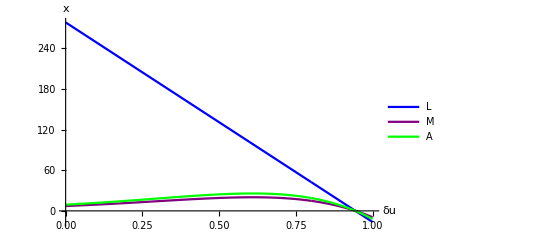

```mathematica
ListLinePlot[
{bifurcationL,bifurcationM,bifurcationA},
PlotStyle->{Blue,Purple,Green},
PlotLegends->{"L","M","A"},
AxesLabel->{"δu","x"},PlotRange->All]
```

```mathematica
ListLinePlot[
{bifurcationL,bifurcationM,bifurcationA},
PlotStyle->{Blue,Purple,Green},
PlotLegends->{"L","M","A"},
AxesLabel->{"δu","x"},PlotRange->All]
```

-Graphics-

## Diagramme de Bifurcation Analytique δa

## Diagramme de Bifurcation Analytique tout les δ pour L

### Paramètres

```mathematica
τuN=4.72;τlN=16;τmN=8.92;αlN=0.001;δuN=0.0432;δlN=0.0048;δmN=0.0150;δaN=1/12.2;qN=106.4/12.2;
```

### Initialisation

```mathematica
UeqNnTriV = LeqNnTri/.{δl -> δlN, δm -> δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->qN,δa->δaN,αl->αlN,q->qN}
LeqNnTriV = LeqNnTri/.{δu -> δuN, δm -> δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->qN,δa->δaN,αl->αlN,q->qN}
MeqNnTriV = LeqNnTri/.{δl -> δlN, δu -> δuN,τu -> τuN, τl -> τlN, τm-> τmN,q->qN,δa->δaN,αl->αlN,q->qN}
AeqNnTriV = LeqNnTri/.{δl -> δlN, δm -> δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->qN,δu->δuN,αl->αlN,q->qN}
```

62.5 (4.45661-4.72 δu)

62.5 (4.3295-16 δl)

62.5 (4.3865-8.92 δm)

253.366

```mathematica
LeqNnTri
```

(-δl τl-δm τm-δu τu-Log[0.1/q])/(αl τl)

```mathematica
bifurcationU=Table[
{δu, UeqNnTriV},
{δu,0.01,1,0.0001}
]
bifurcationL=Table[
{δl, LeqNnTriV},
{δl,0.001,1,0.0001}
];
bifurcationM=Table[
{δm, MeqNnTriV},
{δm,0.001,1,0.0001}
];
bifurcationA=Table[
{δa, AeqNnTriV},
{δa,0.001,1,0.0001}
];
```

{{0.01,275.588},{0.0101,275.558},{0.0102,275.529},{0.0103,275.499},{0.0104,275.47},{0.0105,275.44},{0.0106,275.411},{0.0107,275.381},{0.0108,275.352},{0.0109,275.322},{0.011,275.293},{0.0111,275.263},{0.0112,275.234},9876,{0.9989,-16.1377},{0.999,-16.1672},{0.9991,-16.1967},{0.9992,-16.2262},{0.9993,-16.2557},{0.9994,-16.2852},{0.9995,-16.3147},{0.9996,-16.3442},{0.9997,-16.3737},{0.9998,-16.4032},{0.9999,-16.4327},{1.,-16.4622}}
 |  |  |  |

```mathematica
Export["/Users/Quentin/Desktop/Article1/tables/sansPara/BifucationU_Mathematica.csv",bifurcationU,"CSV"]
Export["/Users/Quentin/Desktop/Article1/tables/sansPara/BifucationL_Mathematica.csv",bifurcationL,"CSV"]
Export["/Users/Quentin/Desktop/Article1/tables/sansPara/BifucationM_Mathematica.csv",bifurcationM,"CSV"]
Export["/Users/Quentin/Desktop/Article1/tables/sansPara/BifucationA_Mathematica.csv",bifurcationA,"CSV"]
```

/Users/Quentin/Desktop/Article1/tables/sansPara/BifucationU_Mathematica.csv

/Users/Quentin/Desktop/Article1/tables/sansPara/BifucationL_Mathematica.csv

/Users/Quentin/Desktop/Article1/tables/sansPara/BifucationM_Mathematica.csv

/Users/Quentin/Desktop/Article1/tables/sansPara/BifucationA_Mathematica.csv

### Paramètres

```mathematica
τuN=4.72;τlN=16;τmN=8.92;αlN=0.001;δuN=0.0432;δlN=0.0048;δmN=0.0150;δaN=1/12.2;qN=106.4/12.2;
```

### Initialisation

```mathematica
UeqNnTriV = UeqNnTri/.{δl -> δlN, δm -> δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->qN,δu->δuN,αl->αlN,q->qN}
LeqNnTriV = LeqNnTri/.{δl -> δlN, δm -> δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->qN,δu->δuN,αl->αlN,q->qN}
MeqNnTriV = MeqNnTri/.{δl -> δlN, δm -> δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->qN,δu->δuN,αl->αlN,q->qN}
AeqNnTriV = AeqNnTri/.{δl -> δlN, δm -> δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->qN,δu->δuN,αl->αlN,q->qN}
```

1733.04

253.366

8.9207

9.34664

```mathematica
bifurcationU=Table[
{δa, UeqNnTriV},
{δa,0.01,8,0.001}
];
bifurcationL=Table[
{δa, LeqNnTriV},
{δa,0.001,8,0.001}
];
bifurcationM=Table[
{δa, MeqNnTriV},
{δa,0.001,8,0.001}
];
bifurcationA=Table[
{δa, AeqNnTriV},
{δa,0.001,8,0.001}
];
```

```mathematica
realData=Select[Flatten[bifurcationU,1],Im[#[[2]]]==0&];
```

Part::partd: Part specification 0.01⟦2⟧ is longer than depth of object.

Part::partd: Part specification 1733.04⟦2⟧ is longer than depth of object.

Part::partd: Part specification 0.011⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

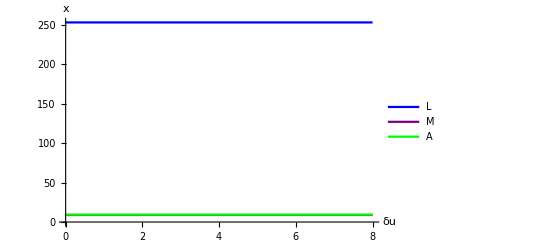

```mathematica
ListLinePlot[
{bifurcationL,bifurcationM,bifurcationA},
PlotStyle->{Blue,Purple,Green},
PlotLegends->{"L","M","A"},
AxesLabel->{"δu","x"},PlotRange->All]
```

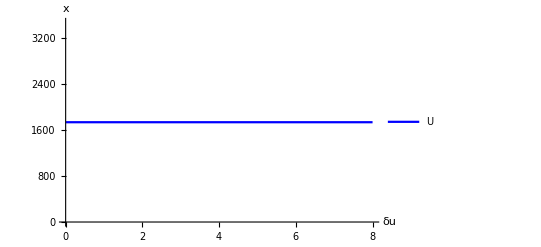

```mathematica
ListLinePlot[
{bifurcationU},
PlotStyle->{Blue,Purple,Green},
PlotLegends->{"U"},
AxesLabel->{"δu","x"},PlotRange->All]
```

## Linéarisation

```mathematica
ModeleLineaire = {
nL'[t] == q nA[t-τu] Exp[-δu τu]- q nA[t-τu-τl] Exp[-δu τu]  Heq -q Aeq Exp[-δu τu]  Hn[t] -(δl+αl nL[t]) Leq-(δl+αl Leq) nL[t],
nA'[t] == q nA[t-τu-τl-τm] Exp[-δu τu] Heq Exp[-δm τm]+q Aeq Exp[-δu τu] nH[t- τm]Exp[-δm τm] -δa nA[t],
nH'[t] ==-αl Heq(nL[t]-nL[t-τl])
}
```

{nL'[t]==-Aeq ⅇ^(-δu τu) q Hn[t]+ⅇ^(-δu τu) q nA[t-τu]-ⅇ^(-δu τu) Heq q nA[t-τl-τu]-(Leq αl+δl) nL[t]-Leq (δl+αl nL[t]),nA'[t]==-0.1 nA[t]+ⅇ^(-δm τm-δu τu) Heq q nA[t-τl-τm-τu]+Aeq ⅇ^(-δm τm-δu τu) q nH[t-τm],nH'[t]==-Heq αl (nL[t]-nL[t-τl])}

## Transformation de Laplace

```mathematica
ModeleLaplace = {
-s L[s]+q A[s]Exp[-s τu] Exp[-δu τu]- q A[s] Exp[-s(τu+τl)] Exp[-δu τu]  Heq -q Aeq Exp[-δu τu]  H[s] - δl L[s]-2 αl Leq L[s],
-s A[s]+q A[s] Exp[-s(τu+τl+τm)] Exp[-δu τu] Heq Exp[-δm τm]+q Aeq Exp[-δu τu] H[s]Exp[- s τm]Exp[-δm τm] -δa A[s],
-s H[s]-αl Heq(L[s]-L[s]Exp[-s τl])
}
```

{ⅇ^(-s τu-δu τu) q A[s]-ⅇ^(-δu τu-s (τl+τu)) Heq q A[s]-Aeq ⅇ^(-δu τu) q H[s]-s L[s]-2 Leq αl L[s]-δl L[s],-0.1 A[s]+ⅇ^(-δm τm-δu τu-s (τl+τm+τu)) Heq q A[s]-s A[s]+Aeq ⅇ^(-s τm-δm τm-δu τu) q H[s],-s H[s]-Heq αl (L[s]-ⅇ^(-s τl) L[s])}

## Jacobienne

```mathematica
JacobienneGeneral =  D[ModeleLaplace,{{L[s],A[s], H[s]}}];
MatrixForm[JacobienneGeneral]
```

(-s-2 Leq αl-δl | ⅇ^(-s τu-δu τu) q-ⅇ^(-δu τu-s (τl+τu)) Heq q | -Aeq ⅇ^(-δu τu) q
0 | -0.1+ⅇ^(-δm τm-δu τu-s (τl+τm+τu)) Heq q-s | Aeq ⅇ^(-s τm-δm τm-δu τu) q
-((1-ⅇ^(-s τl)) Heq αl) | 0 | -s)

```mathematica
JacobienneEqNnTri = FullSimplify[JacobienneGeneral/.{Leq->LeqNnTri,Aeq->AeqNnTri, Heq->(HeqNnTri/.Leq ->LeqNnTri)}]
```

{{(-4.60517-1. s τl+δl τl+2. δm τm+2. δu τu+2. Log[1/q])/τl,ⅇ^(-1. s τu) (-0.1 ⅇ^(-s τl+1. δm τm)+(1. ⅇ^(-1. δu τu))/(1/q)^1.),(10. (-2.30259+δm τm+δu τu+Log[1/q]) (-2.30259+δl τl+δm τm+δu τu+Log[1/q]))/((-10.+ⅇ^(1. δm τm+1. δu τu) (1/q)^1.) αl τl^2)},{0,-0.1+0.1 ⅇ^(s (-1. τl-1. τm-1. τu))-s,(ⅇ^(-((s+δm) τm)) (-2.30259+δm τm+δu τu+Log[1/q]) (-2.30259+δl τl+δm τm+δu τu+Log[1/q]))/((αl-(0.1 ⅇ^(δm τm+δu τu) αl)/q) τl^2)},{-0.1 ⅇ^(-s τl+1. δm τm+1. δu τu) (-1.+ⅇ^(s τl)) (1/q)^1. αl,0,-s}}

## *Stabilité*

### Point Fixe trivial

### Point Fixe non trivial

## Équation caractéristique et sa transformation

```mathematica
EquationCaracteristique = Det[JacobienneEqNnTri]
```

-((-0.1+0.1 ⅇ^(s (-1. τl-1. τm-1. τu))-s) s (-4.60517-1. s τl+δl τl+2. δm τm+2. δu τu+2. Log[1/q]))/τl-0.1 ⅇ^(-s τl+1. δm τm+1. δu τu) (-1.+ⅇ^(s τl)) (1/q)^1. αl (-(10. (-0.1+0.1 ⅇ^(s (-1. τl-1. τm-1. τu))-s) (-2.30259+δm τm+δu τu+Log[1/q]) (-2.30259+δl τl+δm τm+δu τu+Log[1/q]))/((-10.+ⅇ^(1. δm τm+1. δu τu) (1/q)^1.) αl τl^2)+(ⅇ^(-((s+δm) τm)-1. s τu) (-0.1 ⅇ^(-s τl+1. δm τm)+(1. ⅇ^(-1. δu τu))/(1/q)^1.) (-2.30259+δm τm+δu τu+Log[1/q]) (-2.30259+δl τl+δm τm+δu τu+Log[1/q]))/((αl-(0.1 ⅇ^(δm τm+δu τu) αl)/q) τl^2))

```mathematica
D[EquationCaracteristique,αl]
```

-0.1 ⅇ^(-s τl+1. δm τm+1. δu τu) (-1.+ⅇ^(s τl)) (1/q)^1. αl ((10. (-0.1+0.1 ⅇ^(s (-1. τl-1. τm-1. τu))-s) (-2.30259+δm τm+δu τu+Log[1/q]) (-2.30259+δl τl+δm τm+δu τu+Log[1/q]))/((-10.+ⅇ^(1. δm τm+1. δu τu) (1/q)^1.) αl^2 τl^2)-(ⅇ^(-((s+δm) τm)-1. s τu) (-0.1 ⅇ^(-s τl+1. δm τm)+(1. ⅇ^(-1. δu τu))/(1/q)^1.) (1-(0.1 ⅇ^(δm τm+δu τu))/q) (-2.30259+δm τm+δu τu+Log[1/q]) (-2.30259+δl τl+δm τm+δu τu+Log[1/q]))/((αl-(0.1 ⅇ^(δm τm+δu τu) αl)/q)^2 τl^2))-0.1 ⅇ^(-s τl+1. δm τm+1. δu τu) (-1.+ⅇ^(s τl)) (1/q)^1. (-(10. (-0.1+0.1 ⅇ^(s (-1. τl-1. τm-1. τu))-s) (-2.30259+δm τm+δu τu+Log[1/q]) (-2.30259+δl τl+δm τm+δu τu+Log[1/q]))/((-10.+ⅇ^(1. δm τm+1. δu τu) (1/q)^1.) αl τl^2)+(ⅇ^(-((s+δm) τm)-1. s τu) (-0.1 ⅇ^(-s τl+1. δm τm)+(1. ⅇ^(-1. δu τu))/(1/q)^1.) (-2.30259+δm τm+δu τu+Log[1/q]) (-2.30259+δl τl+δm τm+δu τu+Log[1/q]))/((αl-(0.1 ⅇ^(δm τm+δu τu) αl)/q) τl^2))

### Focus sur les solution avec Réel Nul

```mathematica
EquationCaracteristiqueI =EquationCaracteristique /.{s->I x}
```

-(ⅈ (-0.1+0.1 ⅇ^(ⅈ x (-1. τl-1. τm-1. τu))-ⅈ x) x (-4.60517-(0.+1. ⅈ) x τl+δl τl+2. δm τm+2. δu τu+2. Log[1/q]))/τl-0.1 ⅇ^(-ⅈ x τl+1. δm τm+1. δu τu) (-1.+ⅇ^(ⅈ x τl)) (1/q)^1. αl (-(10. (-0.1+0.1 ⅇ^(ⅈ x (-1. τl-1. τm-1. τu))-ⅈ x) (-2.30259+δm τm+δu τu+Log[1/q]) (-2.30259+δl τl+δm τm+δu τu+Log[1/q]))/((-10.+ⅇ^(1. δm τm+1. δu τu) (1/q)^1.) αl τl^2)+(ⅇ^(-((ⅈ x+δm) τm)-(0.+1. ⅈ) x τu) (-0.1 ⅇ^(-ⅈ x τl+1. δm τm)+(1. ⅇ^(-1. δu τu))/(1/q)^1.) (-2.30259+δm τm+δu τu+Log[1/q]) (-2.30259+δl τl+δm τm+δu τu+Log[1/q]))/((αl-(0.1 ⅇ^(δm τm+δu τu) αl)/q) τl^2))

```mathematica
eqCaraRe = ComplexExpand[Re[EquationCaracteristiqueI]];
eqCaraIm = ComplexExpand[Im[EquationCaracteristiqueI]];
```

## Étude numérique

## Import et paramètres

### Image

```mathematica
imageOld=Import["/Users/Quentin/Desktop/Mathematica/Modele Generale/FonfDeJulia.pdf",{"PDF"}];
imageOld=imageOld[[1]];
```

```mathematica
image=Import["/Users/Quentin/Desktop/Mathematica/Modeles_Article/Stab_Da_q.png","PNG"]
```

Import::nffil: File /Users/Quentin/Desktop/Mathematica/Modeles_Article/Stab_Da_q.png not found during Import.

$Failed

```mathematica
data=Import["/Users/Quentin/Desktop/Article1/Tables/sansPara/limite_stab_modele0_deltaA_q.csv","CSV"];
```

#### Créer heatmap à l’arrache

```mathematica
Show[HeatMapVar,(*Insère la heatmap en arrière-plan*)ListLinePlot[{},Axes->True,AxesLabel->{Style["q",FontSize->18,Black],(*Axe des abscisses en noir*)Style["δa",FontSize->18,Black] (*Axe des ordonnées en noir*)},Ticks->Automatic,AxesOrigin->{0,0},AspectRatio->1,PlotRange->{{0,70},{0,1}}]]
```

Show::gcomb: Could not combine the graphics objects in Show[HeatMapVar,].

Show[HeatMapVar,-Graphics-]

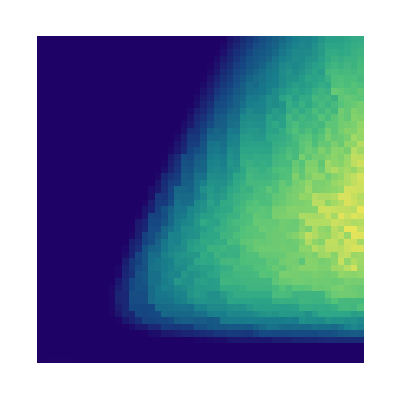

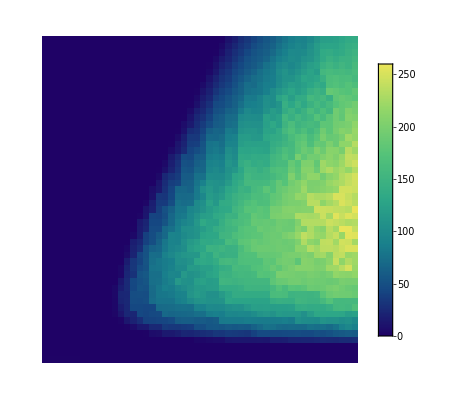

```mathematica
HeatMapVar=ArrayPlot[
data,
ColorFunction->"BlueGreenYellow",(*Palette de couleurs*)
DataReversed->True,
Frame->False,
ImageMargins->0,
PlotRangePadding->0,
AspectRatio->1,
PlotLegends->BarLegend[{"BlueGreenYellow",MinMax[data]},(*Légende associée aux couleurs*)
LabelStyle->{FontSize->15,Black},(*Style des annotations*)
LegendMargins->{{10,10},{10,10}}  (*Marges pour ajuster l'apparence*)]
]
```

-Graphics-

```mathematica
HeatMapVar=ArrayPlot[
data,
ColorFunction->"BlueGreenYellow",
DataReversed->True,
Frame->False,
ImageMargins->0,
PlotRangePadding->0,
AspectRatio->1
]
```

-Graphics-

### Paramètres

```mathematica
τuN=4.72;τlN=16;τmN=8.92;αlN=0.001;δuN=0.0432;δlN=0.0048;δmN=0.0150;
```

### Gamme de δa et q

```mathematica
δaMin =0.001; δaMax = 1; δaPas = 0.001;
qMin =0; qMax = 10; qPas = 0.01;

δaRangeInv=Range[δaMax,δaMin,-δaPas];
δaRange=Range[δaMin,δaMax,δaPas];
qRange=Range[qMin,qMax,qPas];
```

## Limite de stabilité en fonction de δa et q

### Paramétrisation

```mathematica
eqCaraReEq = eqCaraRe /.{τu ->τuN,τl ->τlN,τm ->τmN,αl ->αlN,δu ->δuN,δl->δlN,δm->δmN};
eqCaraImEq = eqCaraIm /.{τu ->τuN,τl ->τlN,τm ->τmN,αl ->αlN,δu ->δuN,δl->δlN,δm->δmN};
```

```mathematica
D[eqCaraReEq,q];
D[eqCaraImEq,q] ;
```

### Tentative de représentation de la manipulation de l’équation caractéristique pour δa

#### Pour la partit réelle

```mathematica
PrepaEqCaraReEq =eqCaraReEq/.{δa->y,q->100};
f[y_,x_]:=PrepaEqCaraReEq
Plot3D[f[y,x],{x,0,10},{y,0,1},PlotLegends->Automatic]
```

-Graphics3D-

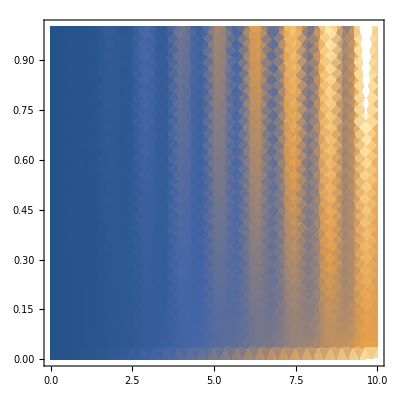

```mathematica
DensityPlot[f[y_,x_],{x,0,10},{y,0,1}]
```

#### Pour la partit imaginaire

```mathematica
PrepaEqCaraImEq =eqCaraImEq/.{δa->y,q->100};
f[y_,x_]:=PrepaEqCaraImEq
Plot3D[f[y_,x_],{x,0,10},{y,0,1}]
```

-Graphics3D-

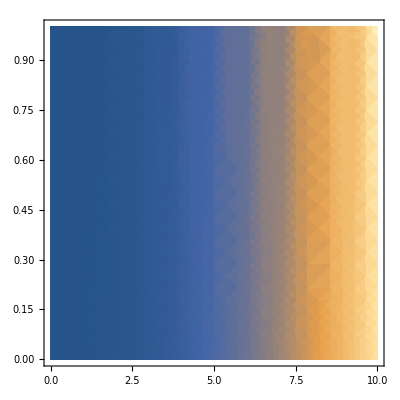

```mathematica
DensityPlot[f[y_,x_],{x,0,10},{y,0,1}]
```

### Tentative de représentation de la manipulation de l’équation caractéristique pour q

#### Pour la partit réelle

```mathematica
PrepaEqCaraReEq =eqCaraReEq/.{δa->1,q->y};
f[y_,x_]:=PrepaEqCaraReEq
Plot3D[f[y_,x_],{y,0,100},{x,0,10},PlotLegends->Automatic]
```

-Graphics3D-

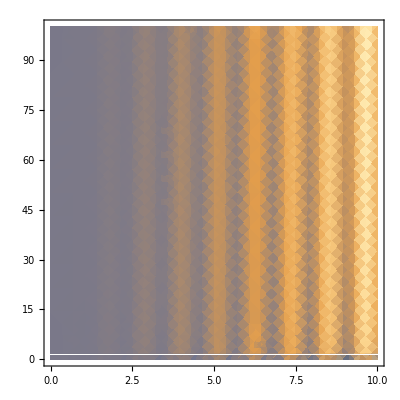

```mathematica
DensityPlot[f[y_,x_],{x,0,10},{y,0,100}]
```

#### Pour la partit imaginaire

```mathematica
PrepaEqCaraImEq =eqCaraImEq/.{δa->1,q->y};
f[y_,x_]:=PrepaEqCaraImEq
Plot3D[f[y_,x_],{x,0,10},{y,0,100}]
```

-Graphics3D-

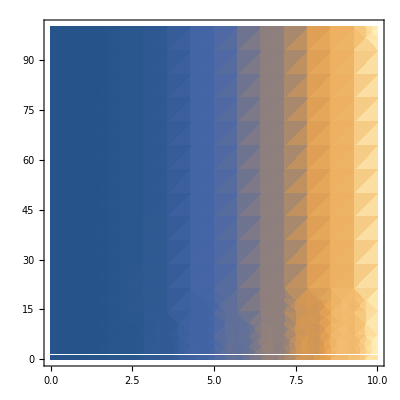

```mathematica
DensityPlot[f[y_,x_],{x,0,10},{y,0,100}]
```

### Tentative de représentation de la manipulation de l’équation caractéristique pour δa et q

#### Pour la partit réelle

-Graphics-

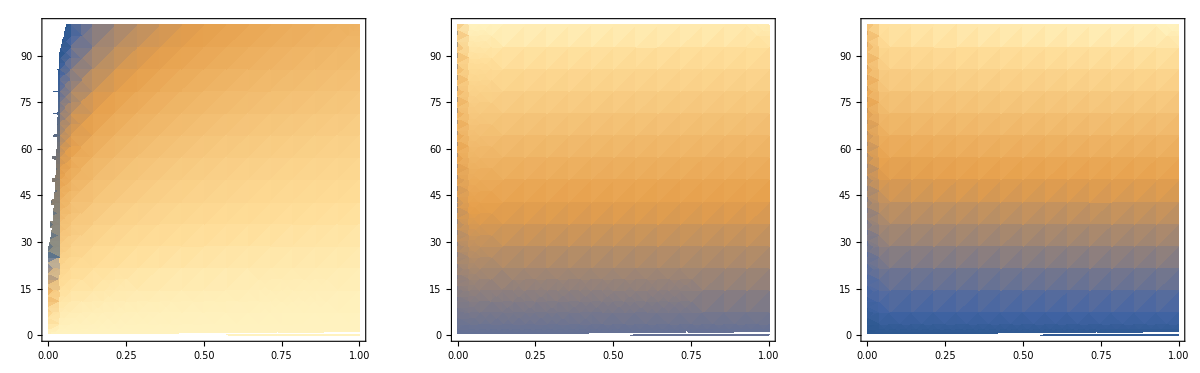

```mathematica
eqCaraReEq1=eqCaraReEq/.{x->0.1};eqCaraReEq2=eqCaraReEq/.{x->1};eqCaraReEq3=eqCaraReEq/.{x->10};
PrepaEqCaraReEq1 =eqCaraReEq1/.{δa->y,q->x};PrepaEqCaraReEq2 =eqCaraReEq2/.{δa->y,q->x};PrepaEqCaraReEq3 =eqCaraReEq3/.{δa->y,q->x};
f[y_,x_]:=PrepaEqCaraReEq1;g[y_,x_]:=PrepaEqCaraReEq2;h[y_,x_]:=PrepaEqCaraReEq3;
GraphicsRow[{
Plot3D[f[x,q],{x,0,1},{y,0,100}],
Plot3D[g[x,q],{x,0,1},{y,0,100}],
Plot3D[h[x,q],{x,0,1},{y,0,100}]
}]
GraphicsRow[{
DensityPlot[f[x,q],{x,0,1},{y,0,100}],
DensityPlot[g[x,q],{x,0,1},{y,0,100}],
DensityPlot[h[x,q],{x,0,1},{y,0,100}]
}]
```

#### Pour la partit imaginaire

-Graphics-

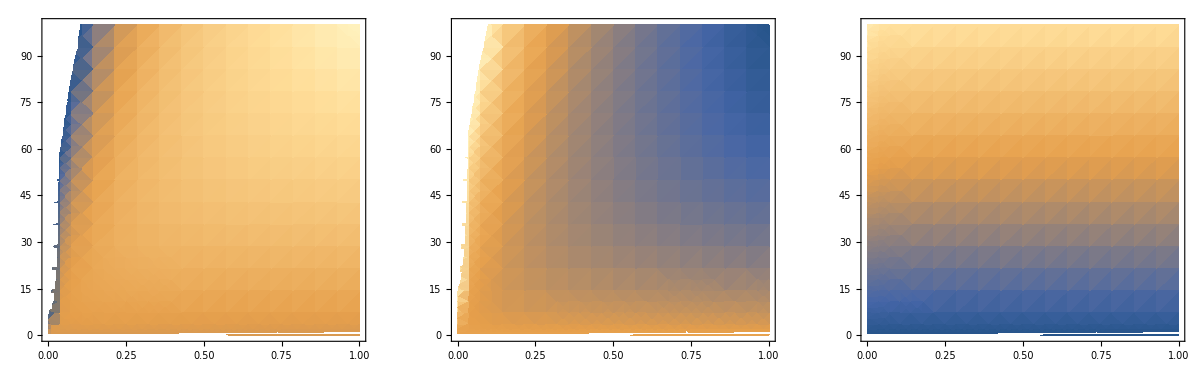

```mathematica
eqCaraImEq1=eqCaraImEq/.{x->0.1};eqCaraImEq2=eqCaraImEq/.{x->1};eqCaraImEq3=eqCaraImEq/.{x->10};
PrepaEqCaraImEq1 =eqCaraImEq1/.{δa->y,q->x};PrepaEqCaraImEq2 =eqCaraImEq2/.{δa->y,q->x};PrepaEqCaraImEq3 =eqCaraImEq3/.{δa->y,q->x};
f[y_,x_]:=PrepaEqCaraImEq1;g[y_,x_]:=PrepaEqCaraImEq2;h[y_,x_]:=PrepaEqCaraImEq3;
GraphicsRow[{
Plot3D[f[x,q],{x,0,1},{y,0,100}],
Plot3D[g[x,q],{x,0,1},{y,0,100}],
Plot3D[h[x,q],{x,0,1},{y,0,100}]
}]
GraphicsRow[{
DensityPlot[f[x,q],{x,0,1},{y,0,100}],
DensityPlot[g[x,q],{x,0,1},{y,0,100}],
DensityPlot[h[x,q],{x,0,1},{y,0,100}]
}]
```

### Recherche de valeur d’initialisation du FindRoot

```mathematica
FindRoot[{eqCaraReEq/.{δa->0.2},eqCaraImEq/.{δa->0.2}},{x,0.13},{q,70}]
FindRoot[{eqCaraReEq/.{δa->0.2},eqCaraImEq/.{δa->0.2}},{x,0.1},{q,1}]
```

{x→0.134856,q→17.0258}

{x→8.48752×10^-9,q→0.302724}

```mathematica
FindRoot[{eqCaraReEq/.{δa->1},eqCaraImEq/.{δa->1}},{x,0.1},{q,30}]
FindRoot[{eqCaraReEq/.{δa->1},eqCaraImEq/.{δa->1}},{x,0.1},{q,1}]
```

{x→0.161159,q→44.0582}

{x→7.88402×10^-9,q→1.51362}

### Création des Courbes

```mathematica
CourbeLimiteCompJulia1 = {}  ;  CourbeLimiteCompJulia2 = {}  ;  
ClearAll[qtempo, xtempo,δa,q,root,  x]
qtempo =30;
xtempo =0.1;
Do [
root = FindRoot[{eqCaraReEq,eqCaraImEq},{x,xtempo},{q,qtempo}];
qtempo = q/.root ;
xtempo = x/.root ;
AppendTo[CourbeLimiteCompJulia1,{qtempo,δa}];
,{δa,δaMax,δaMin,-δaPas}] 

ClearAll[qtempo, xtempo,δa,q,root,  x]
qtempo =1;
xtempo =0.1 ;
Do [
root = FindRoot[{eqCaraReEq,eqCaraImEq},{x,xtempo},{q,qtempo}];
qtempo = q/.root ;
xtempo = x/.root ;
AppendTo[CourbeLimiteCompJulia2,{qtempo,δa}];
,{δa,δaMin,δaMax,δaPas}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::jsing: Encountered a singular Jacobian at the point {x,q} = {0.0764713,5.64685×10^12}. Try perturbing the initial point(s).

General::stop: Further output of FindRoot::jsing will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
Export["/Users/Quentin/Desktop/Article1/tables/limite/sansPara_LimiteStabDeltaA1.csv",CourbeLimiteCompJulia1,"CSV"]
Export["/Users/Quentin/Desktop/Article1/tables/limite/sansPara_LimiteStabDeltaA2.csv",CourbeLimiteCompJulia2,"CSV"]
```

/Users/Quentin/Desktop/Article1/tables/limite/sansPara_LimiteStabDeltaA1.csv

/Users/Quentin/Desktop/Article1/tables/limite/sansPara_LimiteStabDeltaA2.csv

### Affichage des résultats

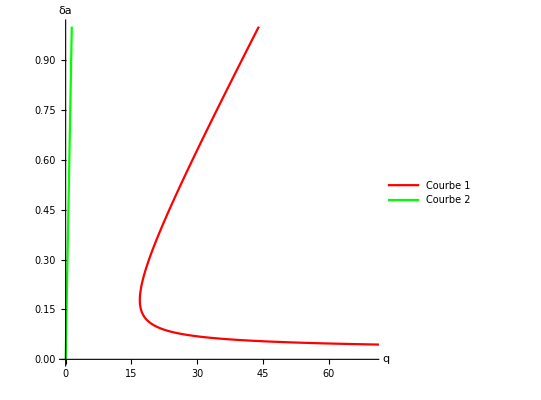

```mathematica
ListLinePlot[{CourbeLimiteCompJulia1,CourbeLimiteCompJulia2},Axes->True,AxesLabel->{Style["q",FontSize->18,Black],(*Axe des abscisses en noir*)Style["δa",FontSize->18,Black] (*Axe des ordonnées en noir*)},PlotLegends->Placed[LineLegend[{"Courbe 1","Courbe 2"},LabelStyle->{FontSize->15,Black}],(*Légendes en noir*){Right,Center}],Ticks->Automatic,AxesOrigin->{0,0},AspectRatio->1,PlotRange->{{0,70},{0,1}},Prolog->{{Inset[HeatMapVar,Scaled[{0,0}],(*Position:centre du graphique*){Left,Bottom},Scaled[{1,2}] (*Taille de l'image par rapport à l'échelle du graphique*)]}},PlotStyle->{Red,Green}]
```

```mathematica
-Graphics--Graphics-
```

-Graphics- -Graphics-

-Graphics-

-Graphics-

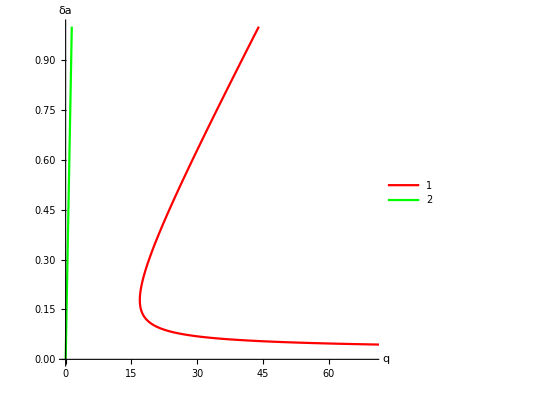

-Graphics-

```mathematica
ListLinePlot[{CourbeLimiteCompJulia1,CourbeLimiteCompJulia2},
Axes->True,
AxesLabel -> {"q","δa"},
PlotLegends -> Automatic,
Ticks->Automatic,
AxesOrigin->{0,0},
AspectRatio-> 1,
PlotRange->{{0,70},{0,1}},
Prolog->{{
Inset[HeatMapVar,(*Image PDF insérée*)
Scaled[{0,0}],(*Position:centre du graphique*)
{Left,Bottom},(*Point d'ancrage de l'image*)
Scaled[{1,2}] (*Taille de l'image par rapport à l'échelle du graphique*)
]
}},
PlotStyle->{Red,Green}
]
```

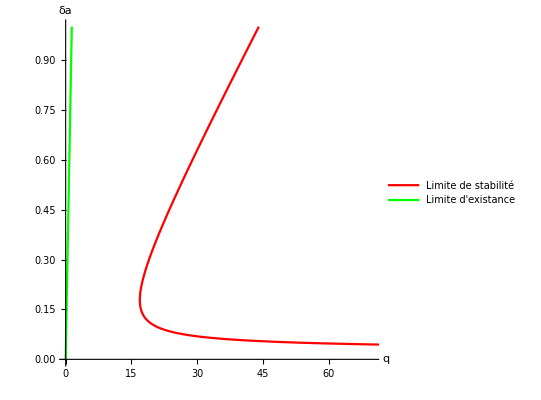

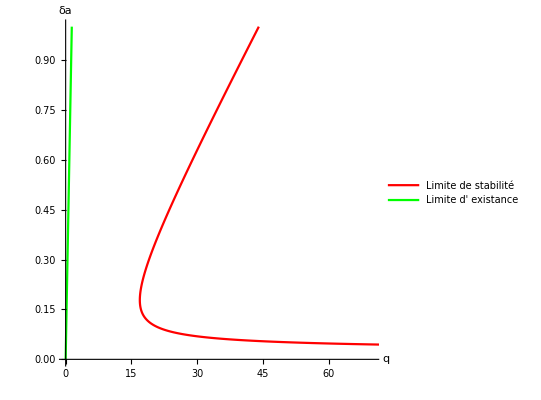

test dynamique sur Julia semble indiquer que pour δa=1 la limite de stab est de q= 43 ce qui corrobore la limite analytique
cependant 2 pb dans la superposition :

## Limite de stabilité en fonction de δu et q

### Paramétrisation

```mathematica
eqCaraReEq = eqCaraRe /.{τu ->τuN,τl ->τlN,τm ->τmN,αl ->αlN,δa ->δaN,δl->δlN,δm->δmN};
eqCaraImEq = eqCaraIm /.{τu ->τuN,τl ->τlN,τm ->τmN,αl ->αlN,δa ->δaN,δl->δlN,δm->δmN};
```

```mathematica
D[eqCaraReEq,q];
D[eqCaraImEq,q] ;
```

### Recherche de valeur d’initialisation du FindRoot

```mathematica
FindRoot[{eqCaraReEq/.{δu->1},eqCaraImEq/.{δu->1}},{x,0.9},{q,1000}]
FindRoot[{eqCaraReEq/.{δu->0.001},eqCaraImEq/.{δu->0.001}},{x,0.1},{q,10}]
```

{x→0.112343,q→2231.7}

{x→0.112343,q→19.9901}

### Création des Courbes

```mathematica
CourbeLimiteCompJulia1 = {}  ;  CourbeLimiteCompJulia2 = {}  ;  
ClearAll[qtempo, xtempo,δu,q,root,  x]
qtempo =0.1;
xtempo =0.1;
Do [
root = FindRoot[{eqCaraReEq,eqCaraImEq},{x,xtempo},{q,qtempo}];
qtempo = q/.root ;
xtempo = x/.root ;
AppendTo[CourbeLimiteCompJulia1,{qtempo,δu}];
,{δu,δaMax,δaMin,-δaPas}] 

ClearAll[qtempo, xtempo,δu,q,root,  x]
qtempo =19.99009603240164;
xtempo =0.11234279129951964 ;
Do [
root = FindRoot[{eqCaraReEq,eqCaraImEq},{x,xtempo},{q,qtempo}];
qtempo = q/.root ;
xtempo = x/.root ;
AppendTo[CourbeLimiteCompJulia2,{qtempo,δu}];
,{δu,δaMin,δaMax,δaPas}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
Export["/Users/Quentin/Desktop/Article1/tables/limite/sansPara_LimiteStabDeltaU1.csv",CourbeLimiteCompJulia1,"CSV"]
Export["/Users/Quentin/Desktop/Article1/tables/limite/sansPara_LimiteStabDeltaU2.csv",CourbeLimiteCompJulia2,"CSV"]
```

/Users/Quentin/Desktop/Article1/tables/limite/sansPara_LimiteStabDeltaU1.csv

/Users/Quentin/Desktop/Article1/tables/limite/sansPara_LimiteStabDeltaU2.csv

```mathematica
"/Users/Quentin/Desktop/Article1/tables/sansPara/LimiteStabDeltaU2.csv"
```

/Users/Quentin/Desktop/Article1/tables/sansPara/LimiteStabDeltaU2.csv

### Affichage des résultats

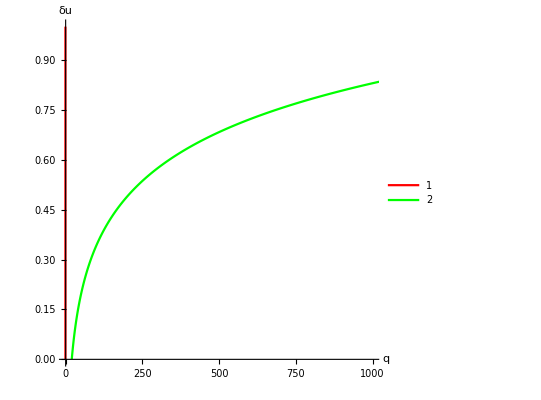

```mathematica
ListLinePlot[{CourbeLimiteCompJulia1,CourbeLimiteCompJulia2},
Axes->True,
AxesLabel -> {"q","δu"},
PlotLegends -> Automatic,
Ticks->Automatic,
AxesOrigin->{0,0},
AspectRatio-> 1,
PlotRange->{{0,1000},{0,1}},
Prolog->{},
PlotStyle->{Red,Green}
]
```

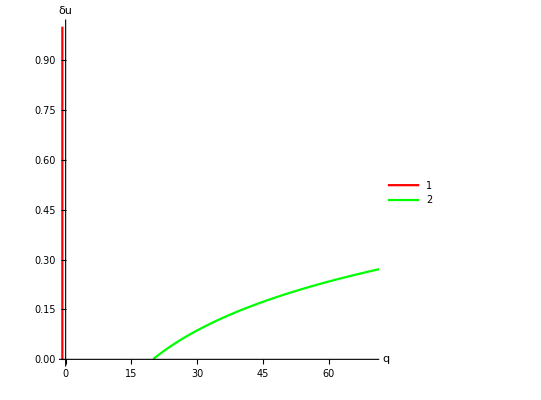

```mathematica
ListLinePlot[{CourbeLimiteCompJulia1,CourbeLimiteCompJulia2},
Axes->True,
AxesLabel -> {"q","δu"},
PlotLegends -> Automatic,
Ticks->Automatic,
AxesOrigin->{0,0},
AspectRatio-> 1,
PlotRange->{{0,70},{0,1}},
Prolog->{},
PlotStyle->{Red,Green}
]
```

Les deux courbes (tracer en partant de 1 ou en partant de 0), se superpose 
C’est une bonne nouvelle

## Limite de stabilité en fonction de δl et q

### Paramétrisation

```mathematica
eqCaraReEq = eqCaraRe /.{τu ->τuN,τl ->τlN,τm ->τmN,αl ->αlN,δa ->δaN,δu->δuN,δm->δmN};
eqCaraImEq = eqCaraIm /.{τu ->τuN,τl ->τlN,τm ->τmN,αl ->αlN,δa ->δaN,δu->δuN,δm->δmN};
```

```mathematica
D[eqCaraReEq,q];
D[eqCaraImEq,q] ;
```

### Recherche de valeur d’initialisation du FindRoot

```mathematica
FindRoot[{eqCaraReEq/.{δl->1},eqCaraImEq/.{δl->1}},{x,0.2},{q,2}]
FindRoot[{eqCaraReEq/.{δl->0.001},eqCaraImEq/.{δl->0.001}},{x,0.14},{q,20}]
```

{x→0.115931,q→0.294571}

{x→0.112331,q→23.62}

### Création des Courbes

```mathematica
CourbeLimiteCompJulia1 = {}  ;  CourbeLimiteCompJulia2 = {}  ;  
ClearAll[qtempo, xtempo,δl,q,root,  x]
qtempo =0.2945713638628388;
xtempo =0.11593085864654919;
Do [
root = FindRoot[{eqCaraReEq,eqCaraImEq},{x,xtempo},{q,qtempo}];
qtempo = q/.root ;
xtempo = x/.root ;
AppendTo[CourbeLimiteCompJulia1,{qtempo,δl}];
,{δl,δaMax,δaMin,-δaPas}] 

ClearAll[qtempo, xtempo,δl,q,root,  x]
qtempo =23.62004562430802;
xtempo =0.1123305294383836 ;
Do [
root = FindRoot[{eqCaraReEq,eqCaraImEq},{x,xtempo},{q,qtempo}];
qtempo = q/.root ;
xtempo = x/.root ;
AppendTo[CourbeLimiteCompJulia2,{qtempo,δl}];
,{δl,δaMin,δaMax,δaPas}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
Export["/Users/Quentin/Desktop/Article1/tables/limite/sansPara_LimiteStabDeltaL1.csv",CourbeLimiteCompJulia1,"CSV"]
Export["/Users/Quentin/Desktop/Article1/tables/limite/sansPara_LimiteStabDeltaL2.csv",CourbeLimiteCompJulia2,"CSV"]
```

/Users/Quentin/Desktop/Article1/tables/limite/sansPara_LimiteStabDeltaL1.csv

/Users/Quentin/Desktop/Article1/tables/limite/sansPara_LimiteStabDeltaL2.csv

### Affichage des résultats

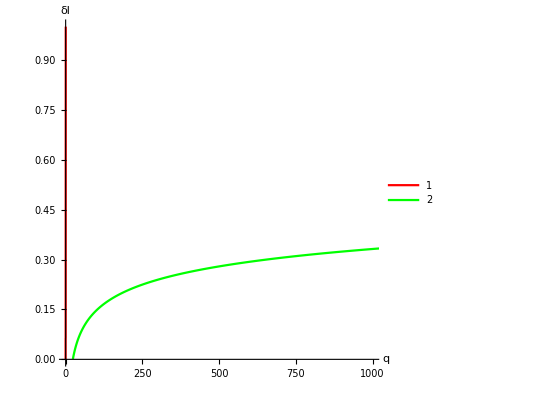

```mathematica
ListLinePlot[{CourbeLimiteCompJulia1,CourbeLimiteCompJulia2},
Axes->True,
AxesLabel -> {"q","δl"},
PlotLegends -> Automatic,
Ticks->Automatic,
AxesOrigin->{0,0},
AspectRatio-> 1,
PlotRange->{{0,1000},{0,1}},
Prolog->{},
PlotStyle->{Red,Green}
]
```

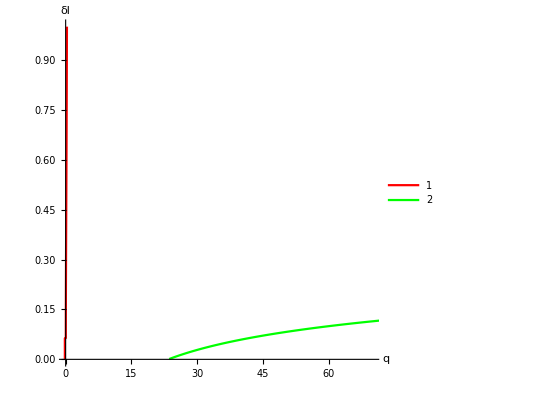

```mathematica
ListLinePlot[{CourbeLimiteCompJulia1,CourbeLimiteCompJulia2},
Axes->True,
AxesLabel -> {"q","δl"},
PlotLegends -> Automatic,
Ticks->Automatic,
AxesOrigin->{0,0},
AspectRatio-> 1,
PlotRange->{{0,70},{0,1}},
Prolog->{},
PlotStyle->{Red,Green}
]
```

Les deux courbes (tracer en partant de 1 ou en partant de 0), se superpose 
C’est une bonne nouvelle

## Limite de stabilité en fonction de δm et q

### Paramétrisation

```mathematica
eqCaraReEq = eqCaraRe /.{τu ->τuN,τl ->τlN,τm ->τmN,αl ->αlN,δa ->δaN,δu->δuN,δl->δlN};
eqCaraImEq = eqCaraIm /.{τu ->τuN,τl ->τlN,τm ->τmN,αl ->αlN,δa ->δaN,δu->δuN,δl->δlN};
```

```mathematica
D[eqCaraReEq,q];
D[eqCaraImEq,q] ;
```

### Recherche de valeur d’initialisation du FindRoot

```mathematica
FindRoot[{eqCaraReEq/.{δm->1},eqCaraImEq/.{δm->1}},{x,1},{q,0.1}]
FindRoot[{eqCaraReEq/.{δm->0.001},eqCaraImEq/.{δm->0.001}},{x,0.14},{q,20}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{x→-0.140351,q→91.7522}

{x→0.112343,q→21.532}

### Création des Courbes

```mathematica
CourbeLimiteCompJulia1 = {}  ;  CourbeLimiteCompJulia2 = {}  ;  
ClearAll[qtempo, xtempo,δm,q,root,  x]
qtempo =0.01;
xtempo =0.1;
Do [
root = FindRoot[{eqCaraReEq,eqCaraImEq},{x,xtempo},{q,qtempo}];
qtempo = q/.root ;
xtempo = x/.root ;
AppendTo[CourbeLimiteCompJulia1,{qtempo,δm}];
,{δm,δaMax,δaMin,-δaPas}] 

ClearAll[qtempo, xtempo,δm,q,root,  x]
qtempo =21.532016188283755;
xtempo =0.112343 ;
Do [
root = FindRoot[{eqCaraReEq,eqCaraImEq},{x,xtempo},{q,qtempo}];
qtempo = q/.root ;
xtempo = x/.root ;
AppendTo[CourbeLimiteCompJulia2,{qtempo,δm}];
,{δm,δaMin,δaMax,δaPas}]
```

FindRoot::jsing: Encountered a singular Jacobian at the point {x,q} = {1.74483×10^-25,473.805}. Try perturbing the initial point(s).

FindRoot::jsing: Encountered a singular Jacobian at the point {x,q} = {6.38356×10^-33,473.805}. Try perturbing the initial point(s).

General::stop: Further output of FindRoot::jsing will be suppressed during this calculation.

General::munfl: -1.91029×10^-80 (-1.12516×10^-239) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
Export["/Users/Quentin/Desktop/Article1/tables/limite/sansPara_LimiteStabDeltaM1.csv",CourbeLimiteCompJulia1,"CSV"]
Export["/Users/Quentin/Desktop/Article1/tables/limite/sansPara_LimiteStabDeltaM2.csv",CourbeLimiteCompJulia2,"CSV"]
```

/Users/Quentin/Desktop/Article1/tables/limite/sansPara_LimiteStabDeltaM1.csv

/Users/Quentin/Desktop/Article1/tables/limite/sansPara_LimiteStabDeltaM2.csv

### Affichage des résultats

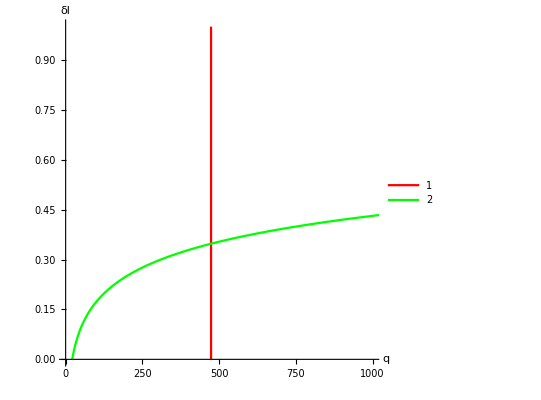

```mathematica
ListLinePlot[{CourbeLimiteCompJulia1,CourbeLimiteCompJulia2},
Axes->True,
AxesLabel -> {"q","δl"},
PlotLegends -> Automatic,
Ticks->Automatic,
AxesOrigin->{0,0},
AspectRatio-> 1,
PlotRange->{{0,1000},{0,1}},
Prolog->{},
PlotStyle->{Red,Green}
]
```

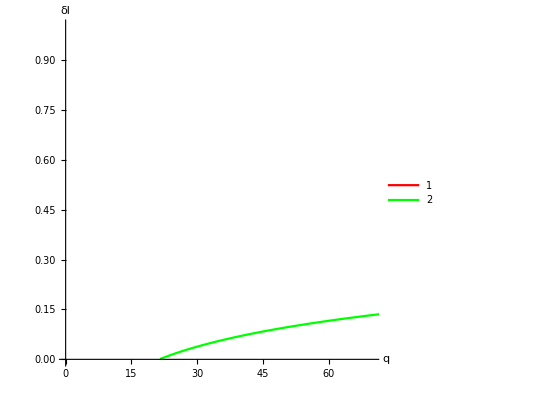

```mathematica
ListLinePlot[{CourbeLimiteCompJulia1,CourbeLimiteCompJulia2},
Axes->True,
AxesLabel -> {"q","δl"},
PlotLegends -> Automatic,
Ticks->Automatic,
AxesOrigin->{0,0},
AspectRatio-> 1,
PlotRange->{{0,70},{0,1}},
Prolog->{},
PlotStyle->{Red,Green}
]
```

Les deux courbes (tracer en partant de 1 ou en partant de 0), se superpose 
C’est une bonne nouvelle

## Dynamiques

## Comparaison de dynamique avec Julia

```mathematica
HeqIni = HeqNnTri/.{Leq->1}//FullSimplify
```

ⅇ^(-((αl+δl) τl))

```mathematica
ⅇ^(-((αl+δl) τl))
HeqIni/.{αl->0.001,τl->τlN,δl->δlN}
```

ⅇ^(-((αl+δl) τl))

0.911376

### Zone Morte

```mathematica
tmax = 10000;
```

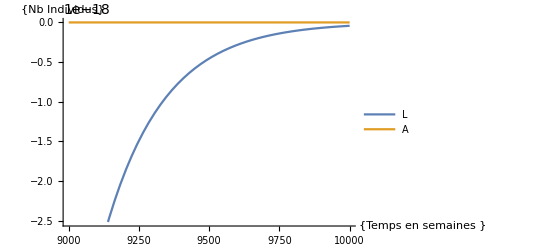

```mathematica
solN=NDSolve[{ModeleReduit/.{δu -> δuN,δl -> δlN, δm -> δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->0.5,δa->0.6,αl->0.001},L[t/;t<=0]==1,A[t/;t<=0]==1, H[t/;t<=0]==HeqIni/.{αl->0.001,τl->τlN,δl->δlN}},{L,A,H},{t,0,tmax}];
Plot[Evaluate[{L[t],A[t]}/. solN],{t,tmax-1000,tmax},PlotLegends->{"L","A"}, AxesLabel->{{"Temps en semaines "},{"Nb Individus"}}]
```

### Zone Stable

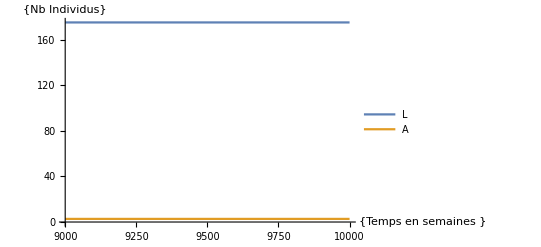

```mathematica
solN=NDSolve[{ModeleReduit/.{δu -> δuN,δl -> δlN, δm -> δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->15,δa->0.6,αl->0.001},L[t/;t<=0]==1,A[t/;t<=0]==1, 
H[t/;t<=0]==HeqIni/.{αl->0.001,τl->τlN,δl->δlN}},{L,A,H},{t,0,tmax}];
Plot[Evaluate[{L[t],A[t]}/. solN],{t,tmax-1000,tmax},PlotLegends->{"L","A"}, AxesLabel->{{"Temps en semaines "},{"Nb Individus"}}]
```

### Zone Instable

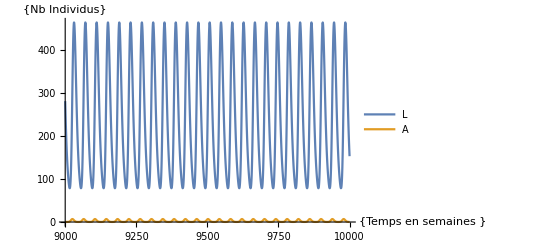

```mathematica
solN=NDSolve[{ModeleReduit/.{δu -> δuN,δl -> δlN, δm -> δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->40,δa->0.6,αl->0.001},L[t/;t<=0]==1,A[t/;t<=0]==1, 
H[t/;t<=0]==HeqIni/.{αl->0.001,τl->τlN,δl->δlN}},{L,A,H},{t,0,tmax}];
Plot[Evaluate[{L[t],A[t]}/. solN],{t,tmax-1000,tmax},PlotLegends->{"L","A"}, AxesLabel->{{"Temps en semaines "},{"Nb Individus"}}]
```

### Testes bordure de stabilité pour δa = 0.6

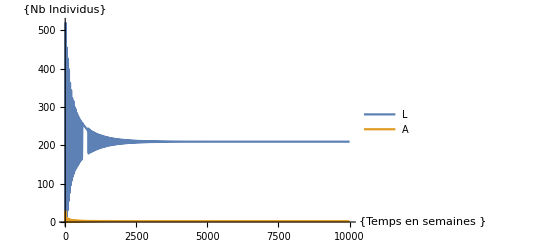

```mathematica
solN=NDSolve[{ModeleReduit/.{δu -> δuN,δl -> δlN, δm -> δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->26,δa->0.6,αl->0.001},L[t/;t<=0]==1,A[t/;t<=0]==1,
H[t/;t<=0]==HeqIni/.{αl->0.001,τl->τlN,δl->δlN}},{L,A,H},{t,0,tmax}];
Plot[Evaluate[{L[t],A[t]}/. solN],{t,0,tmax},PlotLegends->{"L","A"}, AxesLabel->{{"Temps en semaines "},{"Nb Individus"}}]
```

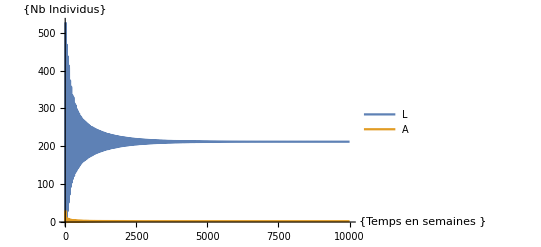

```mathematica
solN=NDSolve[{ModeleReduit/.{δu -> δuN,δl -> δlN, δm -> δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->27,δa->0.6,αl->0.001},L[t/;t<=0]==1,A[t/;t<=0]==1,
H[t/;t<=0]==HeqIni/.{αl->0.001,τl->τlN,δl->δlN}},{L,A,H},{t,0,tmax}];
Plot[Evaluate[{L[t],A[t]}/. solN],{t,0,tmax},PlotLegends->{"L","A"}, AxesLabel->{{"Temps en semaines "},{"Nb Individus"}}]
```

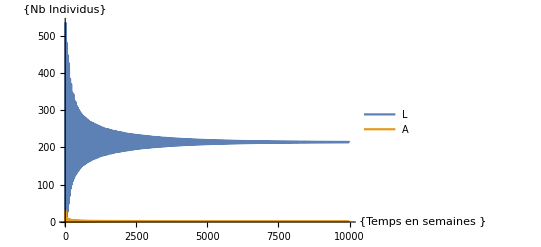

```mathematica
solN=NDSolve[{ModeleReduit/.{δu -> δuN,δl -> δlN, δm -> δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->28,δa->0.6,αl->0.001},L[t/;t<=0]==1,A[t/;t<=0]==1,
H[t/;t<=0]==HeqIni/.{αl->0.001,τl->τlN,δl->δlN}},{L,A,H},{t,0,tmax}];
Plot[Evaluate[{L[t],A[t]}/. solN],{t,0,tmax},PlotLegends->{"L","A"}, AxesLabel->{{"Temps en semaines "},{"Nb Individus"}}]
```

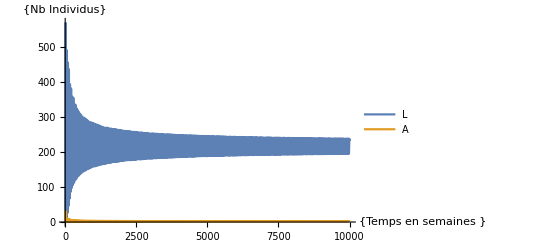

```mathematica
solN=NDSolve[{ModeleReduit/.{δu -> δuN,δl -> δlN, δm -> δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->29,δa->0.6,αl->0.001},L[t/;t<=0]==1,A[t/;t<=0]==1,
H[t/;t<=0]==HeqIni/.{αl->0.001,τl->τlN,δl->δlN}},{L,A,H},{t,0,tmax}];
Plot[Evaluate[{L[t],A[t]}/. solN],{t,0,tmax},PlotLegends->{"L","A"}, AxesLabel->{{"Temps en semaines "},{"Nb Individus"}}]
```

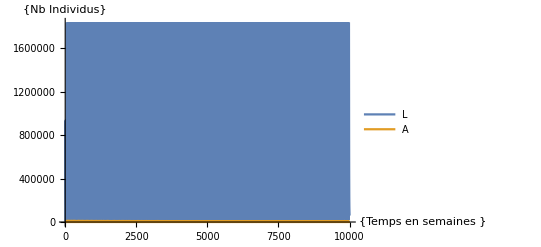

```mathematica
solN=NDSolve[{ModeleReduit/.{δu -> δuN,δl -> δlN, δm -> δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->1000,δa->0.6,αl->0.000001},L[t/;t<=0]==1,A[t/;t<=0]==1,
H[t/;t<=0]==HeqIni/.{αl->0.001,τl->τlN,δl->δlN}},{L,A,H},{t,0,tmax}];
Plot[Evaluate[{L[t],A[t]}/. solN],{t,0,tmax},PlotLegends->{"L","A"}, AxesLabel->{{"Temps en semaines "},{"Nb Individus"}}]
```

#### Dynamique modèle alternatif Quentin

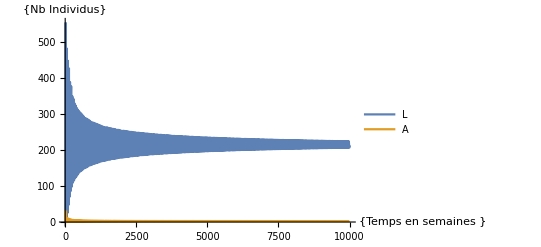

```mathematica
solN=NDSolve[{ModeleReduitQ/.{δu -> δuN,δl -> δlN, δm -> δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->26,δa->0.6,αl->0.001},L[t/;t<=0]==1,A[t/;t<=0]==1, H[t/;t<=0]==0},{L,A,H},{t,0,tmax}];
Plot[Evaluate[{L[t],A[t]}/. solN],{t,0,tmax},PlotLegends->{"L","A"}, AxesLabel->{{"Temps en semaines "},{"Nb Individus"}}]
```

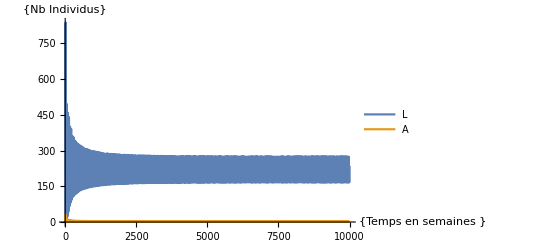

```mathematica
solN=NDSolve[{ModeleReduitQ/.{δu -> δuN,δl -> δlN, δm -> δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->27,δa->0.6,αl->0.001},L[t/;t<=0]==1,A[t/;t<=0]==1, H[t/;t<=0]==0},{L,A,H},{t,0,tmax}];
Plot[Evaluate[{L[t],A[t]}/. solN],{t,0,tmax},PlotLegends->{"L","A"}, AxesLabel->{{"Temps en semaines "},{"Nb Individus"}}]
```

#### Dynamique modèle classique Initialisé avec les valeurs à l’équilibre

```mathematica
LeqNnTriN = LeqNnTri/.{δu -> δuN,δl -> δlN, δm -> δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->26,δa->0.6,αl->0.001}
AeqNnTriN = AeqNnTri/.{δu -> δuN,δl -> δlN, δm -> δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->26,δa->0.6,αl->0.001}
HeqNnTriN = HeqNnTri/.{Leq->LeqNnTriN,δu -> δuN,δl -> δlN, δm -> δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->26,δa->0.6,αl->0.001}
```

209.651

2.19123

0.0323475

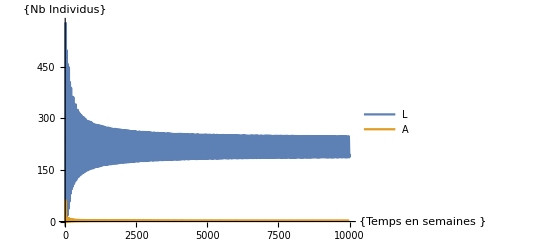

```mathematica
solN=NDSolve[{ModeleReduit/.{δu -> δuN,δl -> δlN, δm -> δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->26,δa->0.6,αl->0.001},L[t/;t<=0]==2,A[t/;t<=0]==2, H[t/;t<=0]==1},{L,A,H},{t,0,tmax}];
Plot[Evaluate[{L[t],A[t]}/. solN],{t,0,tmax},PlotLegends->{"L","A"}, AxesLabel->{{"Temps en semaines "},{"Nb Individus"}}]
```

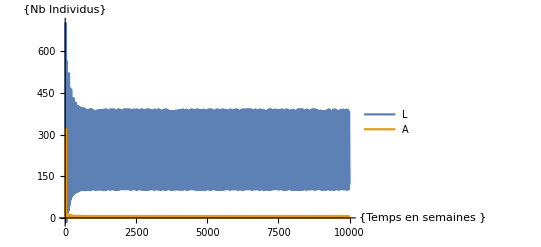

```mathematica
solN=NDSolve[{ModeleReduit/.{δu -> δuN,δl -> δlN, δm -> δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->27,δa->0.6,αl->0.001},L[t/;t<=0]==10,A[t/;t<=0]==10, H[t/;t<=0]==1},{L,A,H},{t,0,tmax}];
Plot[Evaluate[{L[t],A[t]}/. solN],{t,0,tmax},PlotLegends->{"L","A"}, AxesLabel->{{"Temps en semaines "},{"Nb Individus"}}]
```

### Testes bordure de stabilité pour δa = 1

#### Valeur estimé par FindRoot de la limite de stabilité

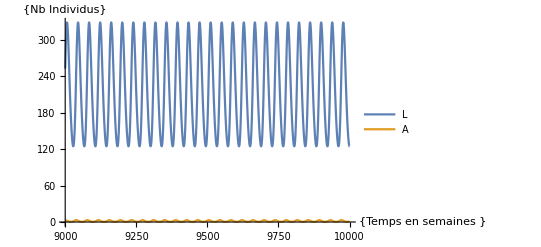

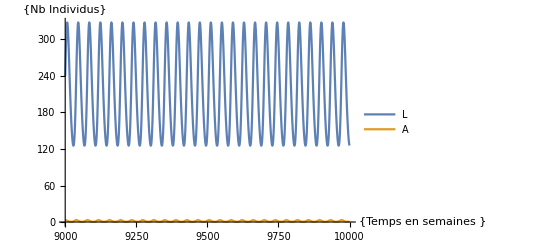

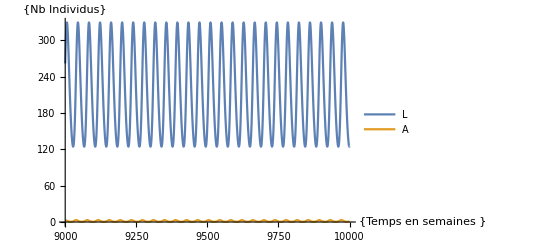

```mathematica
solN=NDSolve[{ModeleReduit/.{δu -> δuN,δl -> δlN, δm -> δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->44.058159856635825,δa->1,αl->0.001},L[t/;t<=0]==1,A[t/;t<=0]==1, H[t/;t<=0]==1},{L,A,H},{t,0,tmax}];
PlotPile = Plot[Evaluate[{L[t],A[t]}/. solN],{t,tmax-1000,tmax},PlotLegends->{"L","A"}, AxesLabel->{{"Temps en semaines "},{"Nb Individus"}}]
solN=NDSolve[{ModeleReduit/.{δu -> δuN,δl -> δlN, δm -> δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->44,δa->1,αl->0.001},L[t/;t<=0]==1,A[t/;t<=0]==1, H[t/;t<=0]==1},{L,A,H},{t,0,tmax}];
PlotDessous = Plot[Evaluate[{L[t],A[t]}/. solN],{t,tmax-1000,tmax},PlotLegends->{"L","A"}, AxesLabel->{{"Temps en semaines "},{"Nb Individus"}}]
solN=NDSolve[{ModeleReduit/.{δu -> δuN,δl -> δlN, δm -> δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->44.1,δa->1,αl->0.001},L[t/;t<=0]==1,A[t/;t<=0]==1, H[t/;t<=0]==1},{L,A,H},{t,0,tmax}];
PlotDessus = Plot[Evaluate[{L[t],A[t]}/. solN],{t,tmax-1000,tmax},PlotLegends->{"L","A"}, AxesLabel->{{"Temps en semaines "},{"Nb Individus"}}]
GraphicsRow[{
PlotPile,
PlotDessous,
PlotDessus
}];
```

#### Encadrement de la solution réelle pour nos valeur d’initialisation

```mathematica
tmax= 50000;
```

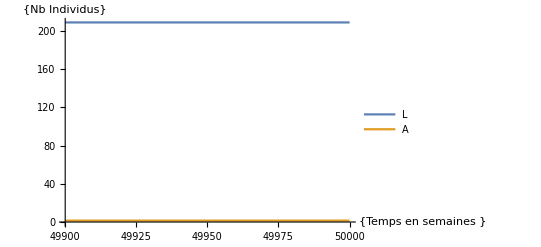

```mathematica
solN=NDSolve[{ModeleReduit/.{δu -> δuN,δl -> δlN, δm -> δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->39,δa->1,αl->0.001},L[t/;t<=0]==1,A[t/;t<=0]==1, H[t/;t<=0]==1},{L,A,H},{t,0,tmax}];
Plot[Evaluate[{L[t],A[t]}/. solN],{t,tmax-100,tmax},PlotLegends->{"L","A"}, AxesLabel->{{"Temps en semaines "},{"Nb Individus"}}]
```

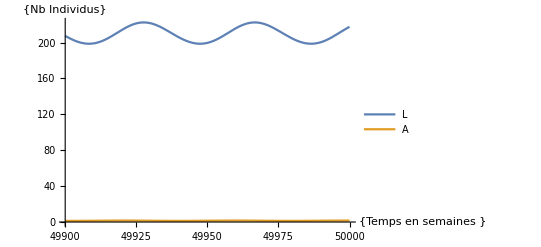

```mathematica
solN=NDSolve[{ModeleReduit/.{δu -> δuN,δl -> δlN, δm -> δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->40,δa->1,αl->0.001},L[t/;t<=0]==1,A[t/;t<=0]==1, H[t/;t<=0]==1},{L,A,H},{t,0,tmax}];
Plot[Evaluate[{L[t],A[t]}/. solN],{t,tmax-100,tmax},PlotLegends->{"L","A"}, AxesLabel->{{"Temps en semaines "},{"Nb Individus"}}]
```

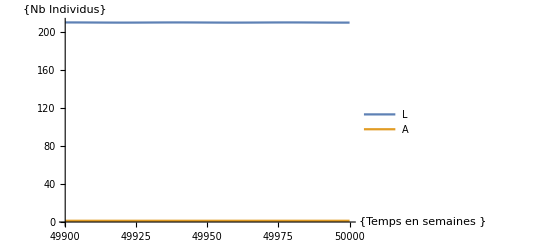

```mathematica
solN=NDSolve[{ModeleReduit/.{δu -> δuN,δl -> δlN, δm -> δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->43.7,δa->1,αl->0.001},L[t/;t<=0]==1,A[t/;t<=0]==1,
H[t/;t<=0]==HeqIni/.{αl->0.001,τl->τlN,δl->δlN}},{L,A,H},{t,0,tmax}];
Plot[Evaluate[{L[t],A[t]}/. solN],{t,tmax-100,tmax},PlotLegends->{"L","A"}, AxesLabel->{{"Temps en semaines "},{"Nb Individus"}}]
```

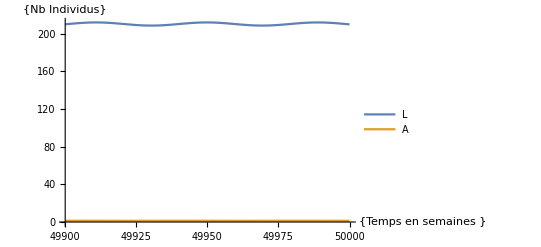

```mathematica
solN=NDSolve[{ModeleReduit/.{δu -> δuN,δl -> δlN, δm -> δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->43.9,δa->1,αl->0.001},L[t/;t<=0]==1,A[t/;t<=0]==1,
H[t/;t<=0]==HeqIni/.{αl->0.001,τl->τlN,δl->δlN}},{L,A,H},{t,0,tmax}];
Plot[Evaluate[{L[t],A[t]}/. solN],{t,tmax-100,tmax},PlotLegends->{"L","A"}, AxesLabel->{{"Temps en semaines "},{"Nb Individus"}}]
```

NICKEL !!!!!!!! 
Les dynamiques sont aligné avec les simuls

```mathematica
HpIniEq = HpEqNnTri/.{Peq->PeqNnTri}
PeqNnTri
HpIniEq = HpIniEq/.{τu ->τuN,τl ->τlN,τm ->τmN,αl ->αlN,δa ->1,δl->δlN,δm->δmN}
```

HpEqNnTri

PeqNnTri

HpEqNnTri

```mathematica
solN=NDSolve[{ModeleReduit/.{δu -> δuN,δl -> δlN, δm -> δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->60,δa->1,αl->0.001},L[t/;t<=0]==1,A[t/;t<=0]==1,
H[t/;t<=0]==HpIniEq/.{q->60}},{L,A,H},{t,0,tmax}];
Plot[Evaluate[{L[t],A[t]}/. solN],{t,tmax-1000,tmax},PlotLegends->{"L","A"}, AxesLabel->{{"Temps en semaines "},{"Nb Individus"}}]
```

NDSolve::ndinnt: Initial condition HpEqNnTri is not a number or a rectangular array of numbers.

ReplaceAll::reps: {NDSolve[{{L'[t]==48.9324 A[«1»]-48.9324 A[«1»] H[«1»]-Plus[«2»] L[«1»],A'[t]==-A[«1»]+42.8044 A[«1»] H[«1»],H'[t]==-0.001 H[t] (Times[«2»]+L[«1»])},L[t/;t≤0]==1,A[t/;t≤0]==1,H[t/;t≤0]==HpEqNnTri},{L,A,H},{t,0,50000}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 49000. cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{{L'[49000.]==48.9324 A[«1»]-48.9324 A[«1»] H[«1»]-Plus[«2»] L[«1»],A'[49000.]==-A[«1»]+42.8044 A[«1»] H[«1»],H'[49000.]==-0.001 H[49000.] (Times[«2»]+L[«1»])},L[49000./;t≤0]==1,A[49000./;t≤0]==1,H[49000./;t≤0]==HpEqNnTri},{L,A,H},{49000.,0,50000}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 49000. cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{{L'[49000.]==48.9324 A[«1»]-48.9324 A[«1»] H[«1»]-1. Plus[«2»] L[«1»],A'[49000.]==-1. A[«1»]+42.8044 A[«1»] H[«1»],H'[49000.]==-0.001 H[49000.] (Times[«2»]+L[«1»])},L[49000./;t≤0.]==1.,A[49000./;t≤0.]==1.,H[49000./;t≤0.]==HpEqNnTri},{L,A,H},{49000.,0.,50000.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 49020.4 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

-Graphics-

```mathematica
solN=NDSolve[{ModeleReduit/.{δu -> δuN,δl -> δlN, δm -> δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->20,δa->1,αl->0.001},L[t/;t<=0]==1,A[t/;t<=0]==1,
H[t/;t<=0]==HpIniEq/.{q->40}},{L,A,H},{t,0,tmax}];
Plot[Evaluate[{L[t],A[t]}/. solN],{t,tmax-1000,tmax},PlotLegends->{"L","A"}, AxesLabel->{{"Temps en semaines "},{"Nb Individus"}}]
```

NDSolve::ndinnt: Initial condition HpEqNnTri is not a number or a rectangular array of numbers.

ReplaceAll::reps: {NDSolve[{{L'[t]==16.3108 A[«1»]-16.3108 A[«1»] H[«1»]-Plus[«2»] L[«1»],A'[t]==-A[«1»]+14.2681 A[«1»] H[«1»],H'[t]==-0.001 H[t] (Times[«2»]+L[«1»])},L[t/;t≤0]==1,A[t/;t≤0]==1,H[t/;t≤0]==HpEqNnTri},{L,A,H},{t,0,50000}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 49000. cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{{L'[49000.]==16.3108 A[«1»]-16.3108 A[«1»] H[«1»]-Plus[«2»] L[«1»],A'[49000.]==-A[«1»]+14.2681 A[«1»] H[«1»],H'[49000.]==-0.001 H[49000.] (Times[«2»]+L[«1»])},L[49000./;t≤0]==1,A[49000./;t≤0]==1,H[49000./;t≤0]==HpEqNnTri},{L,A,H},{49000.,0,50000}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 49000. cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{{L'[49000.]==16.3108 A[«1»]-16.3108 A[«1»] H[«1»]-1. Plus[«2»] L[«1»],A'[49000.]==-1. A[«1»]+14.2681 A[«1»] H[«1»],H'[49000.]==-0.001 H[49000.] (Times[«2»]+L[«1»])},L[49000./;t≤0.]==1.,A[49000./;t≤0.]==1.,H[49000./;t≤0.]==HpEqNnTri},{L,A,H},{49000.,0.,50000.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 49020.4 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

-Graphics-

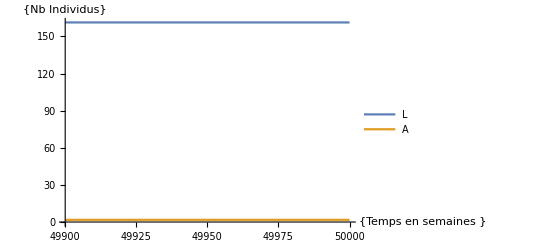

```mathematica
solN=NDSolve[{ModeleReduit/.{δu -> 0.0432,δl -> 0.0048, δm -> 0.0150,τu -> 4.72, τl -> 16, τm-> 8.92,q->20,δa->1,αl->0.001},L[t/;t<=0]==1,A[t/;t<=0]==1,
H[t/;t<=0]==HeqIni/.{αl->0.001,τl->16,δl->0.0048}},{L,A,H},{t,0,tmax}];
Plot[Evaluate[{L[t],A[t]}/. solN],{t,tmax-100,tmax},PlotLegends->{"L","A"}, AxesLabel->{{"Temps en semaines "},{"Nb Individus"}}]
```